```mathematica
Clear@"`*"
res=Assuming[beta>=0&&t>0&&alpha>0&&a>0,Integrate[Exp[-2a(q-q0)^2]Exp[-2((1+q^2- b q)alpha+beta b q) t],{q,-Infinity,Infinity}]]
```

(ⅇ^((t (-4 a (b beta q0+alpha (1-b q0+q0^2))+(alpha^2 (-4+b^2)-2 alpha b^2 beta+b^2 beta^2) t))/(2 (a+alpha t))) √(π/2))/(√(a+alpha t))

```mathematica
res2=res/.b->0
```

(ⅇ^((t (-4 a alpha (1+q0^2)-4 alpha^2 t))/(2 (a+alpha t))) √(π/2))/(√(a+alpha t))

```mathematica
alpha^2 (-4+b^2)-2 alpha b^2 beta+b^2 beta^2//FullSimplify
```

(alpha (-2+b)-b beta) (alpha (2+b)-b beta)

```mathematica
FullSimplify[1/(2 (a+alpha t))t (-4 a (b beta q0+alpha (1-b q0+q0^2))+(alpha^2 (-4+b^2)-2 alpha b^2 beta+b^2 beta^2) t)/.beta->alpha]
```

-(2 alpha t (a+a q0^2+alpha t))/(a+alpha t)

```mathematica
res5=(alpha (-2+b)-b beta) (alpha (2+b)-b beta)/.alpha->0.02
```

(0.02 (-2+b)-b beta) (0.02 (2+b)-b beta)

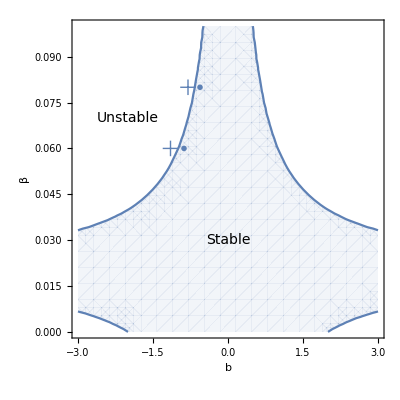

```mathematica
fig=Show[RegionPlot[res5<0,{b,-3,3},{beta,0.0,0.1},BoundaryStyle->None,PlotStyle->Opacity[0.08],FrameTicksStyle->12,FrameLabel->{b,β},LabelStyle->18],ContourPlot[res5==0,{b,-3,3},{beta,0.0,0.1},PlotLegends->Automatic],
ListPlot[{{-0.8,0.08},{-1.15,0.06}},PlotMarkers->{"+",16}],
ListPlot[{{-0.56,0.08},{-0.88,0.06}},PlotMarkers->{"*",20}],
Graphics[{Text[Style["Stable",FontSize->14],{0,0.03}],Text[Style["Unstable",FontSize->14],{-2,0.07}]}]]
```

```mathematica
filename=FileNameJoin[{NotebookDirectory[],"phase.pdf"}];
Export[filename,fig];
```